```mathematica
assoc=GenAll[3];Length[assoc]
```

15

```mathematica
assoc
```

<|0→<|signature→0,matrix→{{2,0,0},{0,2,0},{0,0,2}},graph→-Graphics-,vertexsets→{{1},{2},{3}},vertices→{1,2,3},edges→{},relations→{},links→{}|>,9→<|signature→9,matrix→{{2,1,0},{1,2,0},{0,0,2}},graph→-Graphics-,vertexsets→{{1},{2},{3}},vertices→{1,2,3},edges→{{1,2}},relations→{},links→{}|>,3→<|signature→3,matrix→{{2,0,1},{0,2,0},{1,0,2}},graph→-Graphics-,vertexsets→{{1},{2},{3}},vertices→{1,2,3},edges→{{1,3}},relations→{},links→{}|>,1→<|signature→1,matrix→{{2,0,0},{0,2,1},{0,1,2}},graph→-Graphics-,vertexsets→{{1},{2},{3}},vertices→{1,2,3},edges→{{2,3}},relations→{},links→{}|>,12→<|signature→12,matrix→{{2,1,1},{1,2,0},{1,0,2}},graph→-Graphics-,vertexsets→{{1},{2},{3}},vertices→{1,2,3},edges→{{1,2},{1,3}},relations→{},links→{}|>,10→<|signature→10,matrix→{{2,1,0},{1,2,1},{0,1,2}},graph→-Graphics-,vertexsets→{{1},{2},{3}},vertices→{1,2,3},edges→{{1,2},{2,3}},relations→{},links→{}|>,4→<|signature→4,matrix→{{2,0,1},{0,2,1},{1,1,2}},graph→-Graphics-,vertexsets→{{1},{2},{3}},vertices→{1,2,3},edges→{{1,3},{2,3}},relations→{},links→{}|>,13→<|signature→13,matrix→{{2,1,1},{1,2,1},{1,1,2}},graph→-Graphics-,vertexsets→{{1},{2},{3}},vertices→{1,2,3},edges→{{1,2},{1,3},{2,3}},relations→{},links→{}|>,18→<|signature→18,matrix→{{2,2,0},{2,2,0},{0,0,2}},graph→-Graphics-,vertexsets→{{3},{1,2}},vertices→{1,2},edges→{},relations→{},links→{}|>,22→<|signature→22,matrix→{{2,2,1},{2,2,1},{1,1,2}},graph→-Graphics-,vertexsets→{{3},{1,2}},vertices→{1,2},edges→{{1,2}},relations→{},links→{}|>,26→<|signature→26,matrix→{{2,2,2},{2,2,2},{2,2,2}},graph→-Graphics-,vertexsets→{{1,2,3}},vertices→{1},edges→{},relations→{},links→{}|>,6→<|signature→6,matrix→{{2,0,2},{0,2,0},{2,0,2}},graph→-Graphics-,vertexsets→{{2},{1,3}},vertices→{1,2},edges→{},relations→{},links→{}|>,16→<|signature→16,matrix→{{2,1,2},{1,2,1},{2,1,2}},graph→-Graphics-,vertexsets→{{2},{1,3}},vertices→{1,2},edges→{{1,2}},relations→{},links→{}|>,2→<|signature→2,matrix→{{2,0,0},{0,2,2},{0,2,2}},graph→-Graphics-,vertexsets→{{1},{2,3}},vertices→{1,2},edges→{},relations→{},links→{}|>,14→<|signature→14,matrix→{{2,1,1},{1,2,2},{1,2,2}},graph→-Graphics-,vertexsets→{{1},{2,3}},vertices→{1,2},edges→{{1,2}},relations→{},links→{}|>|>

```mathematica
MatrixForm[{{0,0},{0,2}}]
```

(0 | 0
0 | 2)

```mathematica
newAssoc=CompleteRelations[assoc];Length[newAssoc]
```

{{2,2,0},{2,2,0},{0,0,2}}

18

{{2,1,0},{1,2,0},{0,0,2}}

9

{{2,0,2},{0,2,0},{2,0,2}}

6

{{2,0,1},{0,2,0},{1,0,2}}

3

{{2,0,0},{0,2,2},{0,2,2}}

2

{{2,0,0},{0,2,1},{0,1,2}}

1

{x0==x18+x9,x0==x3+x6,x0==x1+x2}

{{2,2,0},{2,2,0},{0,0,2}}

18

{{2,0,0},{0,2,0},{0,0,2}}

0

{{2,1,2},{1,2,0},{2,0,2}}

15

{{2,1,1},{1,2,0},{1,0,2}}

12

{{2,1,0},{1,2,2},{0,2,2}}

11

{{2,1,0},{1,2,1},{0,1,2}}

10

{x9==x0-x18,x9==x12+x15,x9==x10+x11}

{{2,2,1},{2,2,0},{1,0,2}}

21

{{2,1,1},{1,2,0},{1,0,2}}

12

{{2,0,2},{0,2,0},{2,0,2}}

6

{{2,0,0},{0,2,0},{0,0,2}}

0

{{2,0,1},{0,2,2},{1,2,2}}

5

{{2,0,1},{0,2,1},{1,1,2}}

4

{x3==x12+x21,x3==x0-x6,x3==x4+x5}

{{2,2,0},{2,2,1},{0,1,2}}

19

{{2,1,0},{1,2,1},{0,1,2}}

10

{{2,0,2},{0,2,1},{2,1,2}}

7

{{2,0,1},{0,2,1},{1,1,2}}

4

{{2,0,0},{0,2,2},{0,2,2}}

2

{{2,0,0},{0,2,0},{0,0,2}}

0

{x1==x10+x19,x1==x4+x7,x1==x0-x2}

{{2,2,1},{2,2,0},{1,0,2}}

21

{{2,0,1},{0,2,0},{1,0,2}}

3

{{2,1,2},{1,2,0},{2,0,2}}

15

{{2,1,0},{1,2,0},{0,0,2}}

9

{{2,1,1},{1,2,2},{1,2,2}}

14

{{2,1,1},{1,2,1},{1,1,2}}

13

{x12==-x21+x3,x12==-x15+x9,x12==x13+x14}

{{2,2,0},{2,2,1},{0,1,2}}

19

{{2,0,0},{0,2,1},{0,1,2}}

1

{{2,1,2},{1,2,1},{2,1,2}}

16

{{2,1,1},{1,2,1},{1,1,2}}

13

{{2,1,0},{1,2,2},{0,2,2}}

11

{{2,1,0},{1,2,0},{0,0,2}}

9

{x10==x1-x19,x10==x13+x16,x10==-x11+x9}

{{2,2,1},{2,2,1},{1,1,2}}

22

{{2,1,1},{1,2,1},{1,1,2}}

13

{{2,0,2},{0,2,1},{2,1,2}}

7

{{2,0,0},{0,2,1},{0,1,2}}

1

{{2,0,1},{0,2,2},{1,2,2}}

5

{{2,0,1},{0,2,0},{1,0,2}}

3

{x4==x13+x22,x4==x1-x7,x4==x3-x5}

{{2,2,1},{2,2,1},{1,1,2}}

22

{{2,0,1},{0,2,1},{1,1,2}}

4

{{2,1,2},{1,2,1},{2,1,2}}

16

{{2,1,0},{1,2,1},{0,1,2}}

10

{{2,1,1},{1,2,2},{1,2,2}}

14

{{2,1,1},{1,2,0},{1,0,2}}

12

{x13==-x22+x4,x13==x10-x16,x13==x12-x14}

{{2,2,2},{2,2,2},{2,2,2}}

26

{{2,2,1},{2,2,1},{1,1,2}}

22

{x18==x22+x26}

{{2,2,2},{2,2,2},{2,2,2}}

26

{{2,2,0},{2,2,0},{0,0,2}}

18

{x22==x18-x26}

{}

{{2,2,2},{2,2,2},{2,2,2}}

26

{{2,1,2},{1,2,1},{2,1,2}}

16

{x6==x16+x26}

{{2,2,2},{2,2,2},{2,2,2}}

26

{{2,0,2},{0,2,0},{2,0,2}}

6

{x16==-x26+x6}

{{2,2,2},{2,2,2},{2,2,2}}

26

{{2,1,1},{1,2,2},{1,2,2}}

14

{x2==x14+x26}

{{2,2,2},{2,2,2},{2,2,2}}

26

{{2,0,0},{0,2,2},{0,2,2}}

2

{x14==x2-x26}

15

```mathematica
newAssoc
```

<|0→<|signature→0,matrix→{{2,0},{0,2}},graph→-Graphics-,vertexsets→{{1},{2}},vertices→{1,2},edges→{},relations→{x0==0,x0==x1+x2,x0==x1+x2,x0==0},links→{2,1,2,1}|>,1→<|signature→1,matrix→{{2,1},{1,2}},graph→-Graphics-,vertexsets→{{1},{2}},vertices→{1,2},edges→{{1,2}},relations→{x1==0,x1==x0-x2,x1==x0-x2,x1==0},links→{2,0,2,0}|>,2→<|signature→2,matrix→{{2,2},{2,2}},graph→-Graphics-,vertexsets→{{1,2}},vertices→{1},edges→{},relations→{x2==x0-x1},links→{}|>|>

```mathematica
expr
```

x0==Symbol[xGraphMatrixSignature[{{2, 0}, {0, 2}}, {1}, {1}, 0]]-Symbol[xGraphMatrixSignature[{{2, 0}, {0, 2}}, {1}, {1}, 1]]&&x0==Symbol[xGraphMatrixSignature[{{2, 0}, {0, 2}}, {1}, {2}, 1]]+Symbol[xGraphMatrixSignature[{{2, 0}, {0, 2}}, {1}, {2}, 2]]&&x0==Symbol[xGraphMatrixSignature[{{2, 0}, {0, 2}}, {2}, {1}, 1]]+Symbol[xGraphMatrixSignature[{{2, 0}, {0, 2}}, {2}, {1}, 2]]&&x0==Symbol[xGraphMatrixSignature[{{2, 0}, {0, 2}}, {2}, {2}, 0]]-Symbol[xGraphMatrixSignature[{{2, 0}, {0, 2}}, {2}, {2}, 1]]&&x1==Symbol[xGraphMatrixSignature[{{2, 1}, {1, 2}}, {1}, {1}, 0]]-Symbol[xGraphMatrixSignature[{{2, 1}, {1, 2}}, {1}, {1}, 1]]&&x1==Symbol[xGraphMatrixSignature[{{2, 1}, {1, 2}}, {1}, {2}, 0]]-Symbol[xGraphMatrixSignature[{{2, 1}, {1, 2}}, {1}, {2}, 2]]&&x1==Symbol[xGraphMatrixSignature[{{2, 1}, {1, 2}}, {2}, {1}, 0]]-Symbol[xGraphMatrixSignature[{{2, 1}, {1, 2}}, {2}, {1}, 2]]&&x1==Symbol[xGraphMatrixSignature[{{2, 1}, {1, 2}}, {2}, {2}, 0]]-Symbol[xGraphMatrixSignature[{{2, 1}, {1, 2}}, {2}, {2}, 1]]&&x2==Symbol[xGraphMatrixSignature[{{2, 2}, {2, 2}}, {1, 2}, {1, 2}, 0]]-Symbol[xGraphMatrixSignature[{{2, 2}, {2, 2}}, {1, 2}, {1, 2}, 1]]

```mathematica
expr=Fold[
And,
Monitor[
Table[
With[
{current=newAssoc[key],
rels=newAssoc[key]["relations"],
id=newAssoc[key]["signature"]
},
If[Length[rels]==0,
True
,
Fold[And,rels]
]
]
,
{key,Sort[Keys[newAssoc]]}
],
key]
];Length[expr]
```

9

```mathematica
newAssoc
```

<|0→<|signature→0,matrix→{{2,0},{0,2}},graph→-Graphics-,vertexsets→{{1},{2}},vertices→{1,2},edges→{},relations→{x0==0,x0==x0+x2,x0==x0+x2,x0==0},links→{0,2,0,2}|>,1→<|signature→1,matrix→{{2,1},{1,2}},graph→-Graphics-,vertexsets→{{1},{2}},vertices→{1,2},edges→{{1,2}},relations→{x1==0,x1==x0-x2,x1==x0-x2,x1==0},links→{2,0,2,0}|>,2→<|signature→2,matrix→{{2,2},{2,2}},graph→-Graphics-,vertexsets→{{1,2}},vertices→{1},edges→{},relations→{x2==x0-x1},links→{}|>|>

```mathematica
expr
```

x0==0&&x0==x0+x2&&x0==x0+x2&&x0==0&&x1==0&&x1==x0-x2&&x1==x0-x2&&x1==0&&x2==x0-x1

```mathematica
newAssoc[280]["colofour"]=λ
```

λ

```mathematica
newAssoc[283]["colofour"]=λ-β
```

-β+λ

```mathematica
newAssoc[361]["colofour"]=λ-α
```

-α+λ

```mathematica
newAssoc[442]["colofour"]=α
```

α

```mathematica
newAssoc[286]["colofour"]=β
```

β

```mathematica
newAssoc[448]["colofour"]=α1
```

α1

```mathematica
Map[With[
{num=FromDigits[ StringDrop[SymbolName[#[[1]]],1]],
val=#[[2]]
},
If[KeyExistsQ[newAssoc,num],
newAssoc[num]["colofour"]=val,
Print["Not found ", num, "  ", val]
]
]&,
{x280->λ,x283->λ-β,x361->λ-α,x442->α,x286->β,x448->α1,x367->β-α1,x364->-α+α1-β+λ,x445->α-α1,x365->δ1,x363->-α+α1-β+δ1+λ,x337->δ2,x391->α-α1+β+δ2-λ,x355->δ3,x373->α-α1+β+δ3-λ,x400->δ4,x328->α-α1+β+δ2+δ3+δ4-λ,x121->δ5,x607->α-α1+β+δ5-λ,x606->δ6,x608->-α+α1-β-δ5+δ6+λ,x382->α-α1+β+δ2+δ4-λ,x346->α-α1+β+δ3+δ4-λ,x122->-α+α1-β+δ1-δ5+δ6+λ,x120->-α+α1-β+δ1+δ6+λ}]
```

{λ,-β+λ,-α+λ,α,β,α1,-α1+β,-α+α1-β+λ,α-α1,δ1,-α+α1-β+δ1+λ,δ2,α-α1+β+δ2-λ,δ3,α-α1+β+δ3-λ,δ4,α-α1+β+δ2+δ3+δ4-λ,δ5,α-α1+β+δ5-λ,δ6,-α+α1-β-δ5+δ6+λ,α-α1+β+δ2+δ4-λ,α-α1+β+δ3+δ4-λ,-α+α1-β+δ1-δ5+δ6+λ,-α+α1-β+δ1+δ6+λ}

```mathematica
Reduce[expr]
```

x111==0&&x271==0&&x279==0&&x327==0&&x247==0&&x325==0&&x37==0&&x253==0&&x117==0&&x85==0&&x39==0&&x93==0&&x97==0&&x94==0&&x91==0&&x90==0&&x9==0&&x87==0&&x84==0&&x82==0&&x81==0&&x728==0&&x72==0&&x697==0&&x666==0&&x637==0&&x63==0&&x608==0&&x607==0&&x606==0&&x6==0&&x577==0&&x576==0&&x546==0&&x54==0&&x517==0&&x516==0&&x49==0&&x488==0&&x487==0&&x486==0&&x473==0&&x45==0&&x448==0&&x445==0&&x442==0&&x417==0&&x414==0&&x400==0&&x40==0&&x4==0&&x391==0&&x382==0&&x377==0&&x373==0&&x369==0&&x367==0&&x365==0&&x364==0&&x363==0&&x361==0&&x360==0&&x36==0&&x357==0&&x355==0&&x354==0&&x353==0&&x352==0&&x351==0&&x346==0&&x342==0&&x337==0&&x336==0&&x334==0&&x333==0&&x328==0&&x324==0&&x31==0&&x309==0&&x300==0&&x30==0&&x3==0&&x286==0&&x283==0&&x282==0&&x280==0&&x28==0&&x276==0&&x274==0&&x273==0&&x270==0&&x27==0&&x26==0&&x257==0&&x256==0&&x255==0&&x252==0&&x246==0&&x245==0&&x244==0&&x243==0&&x22==0&&x218==0&&x2==0&&x193==0&&x190==0&&x18==0&&x168==0&&x165==0&&x162==0&&x16==0&&x145==0&&x14==0&&x136==0&&x13==0&&x122==0&&x121==0&&x120==0&&x12==0&&x118==0&&x112==0&&x110==0&&x109==0&&x108==0&&x10==0&&x1==0&&x0==0

```mathematica
exp2=Reduce[expr/.{x280->λ,x283->λ-β,x361->λ-α,x442->α,x286->β,x448->α1,x367->β-α1,x364->-α+α1-β+λ,x445->α-α1,x365->δ1,x363->-α+α1-β+δ1+λ,x337->δ2,x391->α-α1+β+δ2-λ,x355->δ3,x373->α-α1+β+δ3-λ,x400->δ4,x328->α-α1+β+δ2+δ3+δ4-λ,x121->δ5,x607->α-α1+β+δ5-λ,x606->δ6,x608->-α+α1-β-δ5+δ6+λ,x382->α-α1+β+δ2+δ4-λ,x346->α-α1+β+δ3+δ4-λ,x122->-α+α1-β+δ1-δ5+δ6+λ,x120->-α+α1-β+δ1+δ6+λ,x0->δ7,x1->δ8,x3->δ9,x->δ7-δ8},{x10}]
```

x354==-x357+x360+x369&&x352==-x353+x360+x369&&x351==x360+x369&&x273==x30-x516&&x270==x276+x30-x516&&x246==x30+x300-x516&&x282==-x309+x336+x417&&x256==-x257+x336+x417&&x255==x336+x417&&x31==x40+x49&&x274==x40+x49-x517&&x112==-x193+x40+x49&&x333==-x576+x90&&x324==x342-x576+x90&&x252==x414-x576+x90&&x136==x190-x28+x82&&x109==-x190+x28&&x108==x110-x190+x28&&x91==x94+x97&&x334==-x577+x94+x97&&x118==-x145+x94+x97&&x81==x84+x87&&x6==δ7-δ9&&x54==x63+x72&&x486==x487+x488&&x45==-x72-x9+δ7&&x36==-x63+x9&&x27==-x63-x72+δ7&&x245==-x488+δ7-δ8&&x244==-x487+δ8&&x243==-x487-x488+δ7&&x2==δ7-δ8&&x18==-x9+δ7&&x168==-x87+δ7-δ9&&x165==-x84+δ9&&x162==-x84-x87+δ7&&x13==-x22+x4&&x12==x14-x22+x4&&x10==x16-x22+x4

```mathematica
exp3=FullSimplify[exp2];Length[exp3]
```

$Aborted

```mathematica
getAllVariables[exp2]//DeleteDuplicates//Sort
```

{x0,x1,x10,x108,x109,x110,x112,x118,x12,x120,x121,x122,x13,x136,x14,x145,x16,x162,x165,x168,x18,x190,x193,x2,x22,x243,x244,x245,x246,x252,x255,x256,x257,x27,x270,x273,x274,x276,x28,x282,x3,x30,x300,x309,x31,x324,x328,x333,x334,x336,x337,x342,x346,x351,x352,x353,x354,x355,x357,x36,x360,x363,x364,x365,x367,x369,x373,x382,x391,x4,x40,x400,x414,x417,x445,x45,x486,x487,x488,x49,x516,x517,x54,x576,x577,x6,x606,x607,x608,x63,x72,x81,x82,x84,x87,x9,x90,x91,x94,x97,α,α1,β,λ}

```mathematica
headlist={Or,And,Equal,Unequal,Less,LessEqual,Greater,GreaterEqual,Inequality};

getAllVariables[f_?NumericQ]:=Sequence[]
getAllVariables[{}]:=Sequence[]
getAllVariables[t_]/;MemberQ[headlist,t]:=Sequence[]

getAllVariables[ll_List]:=Flatten[Union[Map[getAllVariables[#]&,ll]]]

getAllVariables[Derivative[n_Integer][f_][arg__]]:=getAllVariables[{arg}]

getAllVariables[f_Symbol[arg__]]:=Module[{fvars},If[MemberQ[Attributes[f],NumericFunction]||MemberQ[headlist,f],fvars=getAllVariables[{arg}],(*else*)fvars=f[arg]];
fvars]

getAllVariables[other_]:=other
```

```mathematica
Reduce[exp2,x367]
```

x282==-x309+x336+x417&&x256==-x257+x336+x417&&x255==x336+x417&&x354==-x357+x360+x369&&x352==-x353+x360+x369&&x351==x360+x369&&x91==x94+x97&&x334==-x577+x94+x97&&x118==-x145+x94+x97&&x13==-x22+x4&&x12==x14-x22+x4&&x10==x16-x22+x4&&x273==x30-x516&&x270==x276+x30-x516&&x246==x30+x300-x516&&x136==x190-x28+x82&&x109==-x190+x28&&x108==x110-x190+x28&&x31==x40+x49&&x274==x40+x49-x517&&x112==-x193+x40+x49&&x333==-x576+x90&&x324==x342-x576+x90&&x252==x414-x576+x90&&x81==x84+x87&&x54==x63+x72&&x486==x487+x488&&x36==-x63+x9&&x3==x45-x6+x72+x9&&x27==x45-x63+x9&&x244==-x245+x45-x487-x488+x72+x9&&x243==x45-x487-x488+x72+x9&&x2==x245+x488&&x18==x45+x72&&x168==x6-x87&&x165==x45-x6+x72-x84+x9&&x162==x45+x72-x84-x87+x9&&x1==-x245+x45-x488+x72+x9&&x0==x45+x72+x9&&x606==x607+x608&&x445==α-α1&&x382==x391+x400&&x364==-α+α1-β+λ&&x363==x365-α+α1-β+λ&&x355==x373-α+α1-β+λ&&x346==x373+x400&&x337==x391-α+α1-β+λ&&x328==x373+x391+x400-α+α1-β+λ&&x122==x365+x608&&x121==x607-α+α1-β+λ&&x120==x365+x607+x608-α+α1-β+λ&&x367==-α1+β

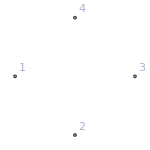
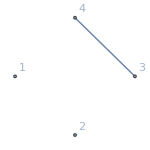
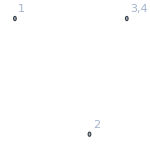
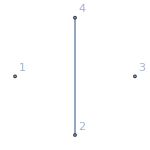
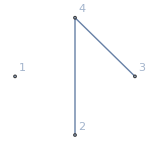
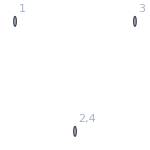
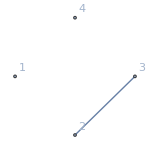
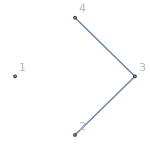
{-Graphics-x0==x243+x486
x0==x162+x81
x0==x27+x54
x0==x18+x9
x0==x3+x6
x0==x1+x20,-Graphics-x1==x244+x487
x1==x0-x21,-Graphics-x2==x245+x488
x2==x0-x12,-Graphics-x3==x165+x84
x3==x0-x63,-Graphics-x4==x13+x224,-Graphics-x6==x168+x87
x6==x0-x36,-Graphics-x9==x36+x63
x9==x0-x189,-Graphics-x10==x13+x1610,-Graphics-x12==x13+x1412,-Graphics-x13==-x22+x4
x13==x10-x16
x13==x12-x1413,-Graphics-x14==x12-x1314,-Graphics-x16==x10-x1316,-Graphics-x18==x45+x72
x18==x0-x918,-Graphics-x22==-x13+x422,-Graphics-{}26,-Graphics-x27==x0-x54
x27==x36+x4527,-Graphics-x28==x109+x19028,-Graphics-x30==x273+x51630,-Graphics-x31==x274+x517
x31==x112+x193
x31==x40+x4931,-Graphics-x36==-x63+x9
x36==x27-x4536,-Graphics-{}37,-Graphics-{}39,-Graphics-x40==x31-x4940,-Graphics-x45==x18-x72
x45==x27-x3645,-Graphics-x49==x31-x4049,-Graphics-x54==x0-x27
x54==x63+x7254,-Graphics-x63==-x36+x9
x63==x54-x7263,-Graphics-x72==x18-x45
x72==x54-x6372,-Graphics-x81==x0-x162
x81==x84+x8781,-Graphics-x82==x109+x13682,-Graphics-x84==-x165+x3
x84==x81-x8784,-Graphics-{}85,-Graphics-x87==-x168+x6
x87==x81-x8487,-Graphics-x90==x333+x57690,-Graphics-x91==x334+x577
x91==x118+x145
x91==x94+x9791,-Graphics-{}93,-Graphics-x94==x91-x9794,-Graphics-x97==x91-x9497,-Graphics-x108==x109+x110108,-Graphics-x109==-x190+x28
x109==-x136+x82
x109==x108-x110109,-Graphics-x110==x108-x109110,-Graphics-{}111,-Graphics-x112==-x193+x31112,-Graphics-{}117,-Graphics-x118==-x145+x91118,-Graphics-x120==x363+x606
x120==x121+x122120→-α+α1-β+δ1+δ6+λ,-Graphics-x121==x364+x607
x121==x120-x122121→δ5,-Graphics-x122==x365+x608
x122==x120-x121122→-α+α1-β+δ1-δ5+δ6+λ,-Graphics-x136==-x109+x82136,-Graphics-x145==-x118+x91145,-Graphics-x162==x0-x81
x162==x165+x168162,-Graphics-x165==x3-x84
x165==x162-x168165,-Graphics-x168==x6-x87
x168==x162-x165168,-Graphics-x190==-x109+x28190,-Graphics-x193==-x112+x31193,-Graphics-{}218,-Graphics-x243==x0-x486
x243==x244+x245243,-Graphics-x244==x1-x487
x244==x243-x245244,-Graphics-x245==x2-x488
x245==x243-x244245,-Graphics-x246==x273+x300246,-Graphics-{}247,-Graphics-x252==x333+x414252,-Graphics-{}253,-Graphics-x255==x336+x417
x255==x282+x309
x255==x256+x257255,-Graphics-x256==x255-x257256,-Graphics-x257==x255-x256257,-Graphics-x270==x273+x276270,-Graphics-{}271,-Graphics-x273==x30-x516
x273==x246-x300
x273==x270-x276273,-Graphics-x274==x31-x517274,-Graphics-x276==x270-x273276,-Graphics-{}279,-Graphics-x280==x361+x442
x280==x283+x286280→λ,-Graphics-x282==x255-x309282,-Graphics-x283==x364+x445
x283==x280-x286283→λ-β,-Graphics-x286==x367+x448
x286==x280-x283286→β,-Graphics-x300==x246-x273300,-Graphics-x309==x255-x282309,-Graphics-x324==x333+x342324,-Graphics-{}325,-Graphics-{}327,-Graphics-x328==x355+x382
x328==x337+x346328→α-α1+β+δ2+δ3+δ4-λ,-Graphics-x333==-x576+x90
x333==x252-x414
x333==x324-x342333,-Graphics-x334==-x577+x91334,-Graphics-x336==x255-x417336,-Graphics-x337==x364+x391
x337==x328-x346337→δ2,-Graphics-x342==x324-x333342,-Graphics-x346==x373+x400
x346==x328-x337346→α-α1+β+δ3+δ4-λ,-Graphics-x351==x360+x369
x351==x354+x357
x351==x352+x353351,-Graphics-x352==x351-x353352,-Graphics-x353==x351-x352353,-Graphics-x354==x351-x357354,-Graphics-x355==x328-x382
x355==x364+x373355→δ3,-Graphics-x357==x351-x354357,-Graphics-x360==x351-x369360,-Graphics-x361==x280-x442
x361==x364+x367361→λ-α,-Graphics-x363==x120-x606
x363==x364+x365363→-α+α1-β+δ1+λ,-Graphics-x364==x121-x607
x364==x283-x445
x364==x337-x391
x364==x355-x373
x364==x361-x367
x364==x363-x365364→-α+α1-β+λ,-Graphics-x365==x122-x608
x365==x363-x364365→δ1,-Graphics-x367==x286-x448
x367==x361-x364367→β-α1,-Graphics-x369==x351-x360369,-Graphics-x373==x346-x400
x373==x355-x364373→α-α1+β+δ3-λ,-Graphics-{}377,-Graphics-x382==x328-x355
x382==x391+x400382→α-α1+β+δ2+δ4-λ,-Graphics-x391==x337-x364
x391==x382-x400391→α-α1+β+δ2-λ,-Graphics-x400==x346-x373
x400==x382-x391400→δ4,-Graphics-x414==x252-x333414,-Graphics-x417==x255-x336417,-Graphics-x442==x280-x361
x442==x445+x448442→α,-Graphics-x445==x283-x364
x445==x442-x448445→α-α1,-Graphics-x448==x286-x367
x448==x442-x445448→α1,-Graphics-{}473,-Graphics-x486==x0-x243
x486==x487+x488486,-Graphics-x487==x1-x244
x487==x486-x488487,-Graphics-x488==x2-x245
x488==x486-x487488,-Graphics-x516==-x273+x30516,-Graphics-x517==-x274+x31517,-Graphics-{}546,-Graphics-x576==-x333+x90576,-Graphics-x577==-x334+x91577,-Graphics-x606==x120-x363
x606==x607+x608606→δ6,-Graphics-x607==x121-x364
x607==x606-x608607→α-α1+β+δ5-λ,-Graphics-x608==x122-x365
x608==x606-x607608→-α+α1-β-δ5+δ6+λ,-Graphics-{}637,-Graphics-{}666,-Graphics-{}697,-Graphics-{}728}

```mathematica
Table[
With[
{current=newAssoc[key]},
Framed[Labeled[Row[{
Graph[current["graph"],ImageSize->{150,150}],
TableForm[current["relations"]]
}
],Style[
If[KeyExistsQ[current,"colofour"],
current["signature"]->TraditionalForm[current["colofour"]],
current["signature"]
],Red]]]
]
,{key,Sort[Keys[newAssoc]]}]
```